## mois

```mathematica
rigid[k_,beta_,gamma_]:=beta^2*Sin[gamma*π/180-2π/3*k]^2;
irrotational[k_,beta_,gamma_]:=1-Sqrt[5/(4π)]beta*Cos[gamma*π/180-2π/3*k];
```

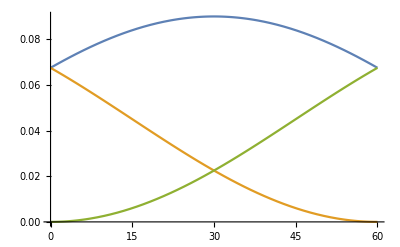

```mathematica
Plot[{rigid[1,0.3,x],rigid[2,0.3,x],rigid[3,0.3,x]},{x,0,60}]
```

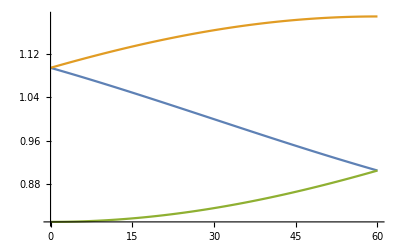

```mathematica
Plot[{irrotational[1,0.3,x],irrotational[2,0.3,x],irrotational[3,0.3,x]},{x,0,60}]
```